# NG4P03. The method Backpropagation.

Выполнила  студентка 2 курса  5 группы
Кадакова Надежда
15.04.2017

## Ex.1

Реализовать процедуру обучения однослойного персептрона методом обратного распространения ошибки

Напишем саму функцию активации.

```mathematica
a=1.7159;
b=2/3;
```

```mathematica
sigm[x_]:=a*Tanh[b*x];
step[x_]:=Sign[x];
```

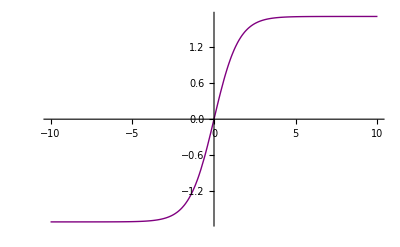

```mathematica
Plot[sigm[x],{x,-10,10},PlotStyle->{Purple,Thick}]
```

Координаты не выпуклового четырехугольника

```mathematica
p1={1.814,-0.608};
p2={-1.162,1.892};
p3={-1.634,-1.884};
p4={-0.85,1.092};
```

```mathematica
CreateLine[{list1_,list2_}]:=(
Clear[x1,x2,y1,y2];
x1=list1⟦1⟧;y1=list1⟦2⟧;
x2=list2⟦1⟧; y2=list2⟦2⟧;
{(y1-y2)/(√((x2-x1)^2+(y2-y1)^2)),(x2-x1)/(√((x2-x1)^2+(y2-y1)^2)),(x1 y2-x2 y1)/(√((x2-x1)^2+(y2-y1)^2))})
```

функции нейрона  и  персептрона

```mathematica
Clear[neuron]
neuron[X_List,W_List,activationfunc_]:=activationfunc[Append[X,1].W]
```

```mathematica
Clear[perceptron]
perceptron[X_,W_,activationfunc_]:=neuron[X,#,activationfunc]&/@W
```

Для возможности применения метода обратного распространения ошибки  функция активации нейронов должна быть дифференцируема

Напишем производную функции активации, выраженную через саму функцию.

```mathematica
Clear[Df]
Df[x_]:=Map[b/a(a+#)(a-#)&,x]
```

## Ex.2

Построить однослойный персептрон с 4 нейронами и обучить его распознаванию четырёх полуплоскостей, определённых следующим образом (см. Рис.1): m-тая полуплоскость содержит точку P_m и имеет границу, проходящую через точки P_(m-1),P_(m+1) . Подготовить графическую анимацию, демонстрирующую процесс обучения.

Хорошие веса

```mathematica
w1=CreateLine[{p4,p2}];
w2=CreateLine[{p1,p3}];
w3=CreateLine[{p2,p4}];
w4=CreateLine[{p3,p1}];
```

для коррекции

```mathematica
w1cor=RandomReal[{-2,2},3];
w2cor=RandomReal[{-1,2},3];
w3cor=RandomReal[{-2,1},3];
w4cor=RandomReal[{-0,2},3];
```

```mathematica
WesaList1={w1,w2,w3,w4}
```

{{-0.931655,-0.363345,-0.395133},{0.347066,-0.937841,-1.19979},{0.931655,0.363345,0.395133},{-0.347066,0.937841,1.19979}}

```mathematica
WesaList2={w1cor,w2cor,w3cor,w4cor}
```

{{-0.817796,1.36982,0.564378},{1.65563,-0.426794,0.00300041},{0.44284,-1.68824,-1.88061},{0.476327,1.70578,1.27303}}

```mathematica
App[otvet_,wesa_,activationfunc_]:=(
Clear[n1,delta,γ1];
res=wesa;
For[i=1,i≤Length[otvet],i++,
n1=neuron[otvet⟦i,1⟧,#,activationfunc]&/@wesa;
γ1=0.5;
δ=(otvet⟦i,2⟧-n1)Df[Append[otvet⟦i,1⟧,1].#&/@wesa];
delta=Append[otvet⟦i,1⟧,1]*#&/@δ;
res=res+γ1*delta];
res
)
```

Учитель.
Узнаём ответы для каждого нейрона каждой точки в 1 слое

```mathematica
teacher={};
Table[AppendTo[teacher,{{i,j},perceptron[{i,j},{w1,w2,w3,w4},sigm]}],{i,-2,2,0.2},{j,-2,2,0.2}];
```

Эпохи

```mathematica
period={};
For[n=1,n≤600,n++,AppendTo[period,RandomSample[teacher]]];
```

Перейдем к реализации
1) найдем 4 ошибки на выходном слое (4 - потому что 4 нейрона)

```mathematica
outmistake=neuron[teacher⟦1,1⟧,#,sigm]&/@WesaList1
```

{1.54136,-0.0208606,-1.54136,0.0208606}

2) для каждого нейрона вычислим ошибку

```mathematica
γ=1;
δ=(teacher⟦1,2⟧-outmistake)Df[Append[teacher⟦1,1⟧,1].#&/@WesaList1]
```

{0.,0.,0.,0.}

3) умножаем на соотв входы:

```mathematica
delta=Append[teacher⟦1,1⟧,1]*#&/@δ
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

4) коррекция весов для слоя следующая:

```mathematica
WesaList1=WesaList1+γ*delta
```

{{-0.931655,-0.363345,-0.395133},{0.347066,-0.937841,-1.19979},{0.931655,0.363345,0.395133},{-0.347066,0.937841,1.19979}}

```mathematica
Function1[wesalist_]:=(
Clear[x,y];
Show[Plot[{Apply[List,Roots[{x,y,1}.wesalist⟦1⟧==0,y]]⟦2⟧,Apply[List,Roots[{x,y,1}.wesalist⟦2⟧==0,y]]⟦2⟧,Apply[List,Roots[{x,y,1}.wesalist⟦3⟧==0,y]]⟦2⟧,Apply[List,Roots[{x,y,1}.wesalist⟦4⟧==0,y]]⟦2⟧},{x,-5,5},PlotRange->{{-2,2},{-2,2}},Filling->Top,GridLines->Automatic],Graphics[{AbsolutePointSize[10],Blue,Point[p1],Point[p2],Point[p3],Point[p4],Red, Point[{1.5,1.5}],Point[{-.5,1}]},GridLines->Automatic]])
```

```mathematica
App[teacher,WesaList2,sigm]
```

{{-327.027,321.463,184.521},{258.117,-76.7105,61.3539},{16.7203,-1529.95,-1044.71},{36.5406,84.6944,62.296}}

```mathematica
List1=Table[WesaList2=App[period⟦i⟧,WesaList2,sigm],{i,1,300}];
```

```mathematica
ListAnimate[Table[Function1[List1[[i]]], {i, 1, 300}], AnimationRate -> 10]
```

правильное положение прямых, согласно принципа, описываемого в задании.

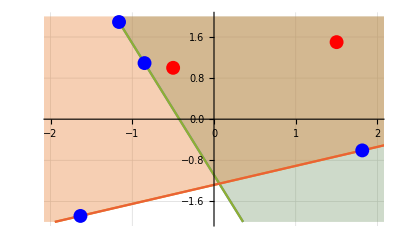

```mathematica
Function1[{w1,w2,w3,w4}]
```

## Ex.3

Реализовать процедуру обучения 2хслойного персептрона методом обратного распространения ошибки

```mathematica
P={p2,p3,p4};
```

Задаем учителя.

```mathematica
coords=Flatten[Table[{i,j},{i,-2,2,0.2},{j,-2,2,0.2}],1];
```

```mathematica
coords[[1]]
```

{-2.,-2.}

```mathematica
Teach111=Table[coords[[i]]->-Sign@SignedRegionDistance[Polygon@P[[]],coords[[i]]],{i,1,Length[coords]}];
```

```mathematica
Teach111[[1]]
```

{-2.,-2.}→-1

Треугольник с вершинами:

```mathematica
App2[wes_]:=(
Clear[x,y];
Show[Plot[{Apply[List,Roots[{x,y,1}.wes⟦1⟧==0,y]]⟦2⟧,Apply[List,Roots[{x,y,1}.wes⟦2⟧==0,y]]⟦2⟧,Apply[List,Roots[{x,y,1}.wes⟦3⟧==0,y]]⟦2⟧},{x,-5,5},PlotRange->{{-5,5},{-5,5}},GridLines->Automatic],Graphics[{AbsolutePointSize[10],Blue,Point[p2],Point[p3],Point[p4]},GridLines->Automatic]])
```

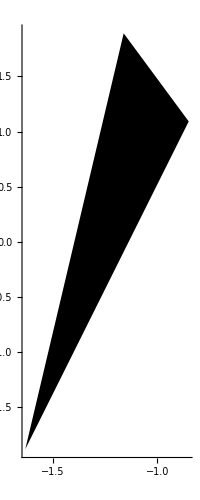

```mathematica
Graphics[Polygon[P],Axes->True]
```

```mathematica
Clear[W1,W2,W3]
```

Рассмотрим первый слой. Веса для нашего треугольника - коэффициенты прямых

```mathematica
W1={CreateLine[{p2,p3}],CreateLine[{p3,p4}],CreateLine[{p4,p2}]}
```

{{0.992278,-0.124035,1.3877},{-0.967007,0.254749,-1.10014},{-0.931655,-0.363345,-0.395133}}

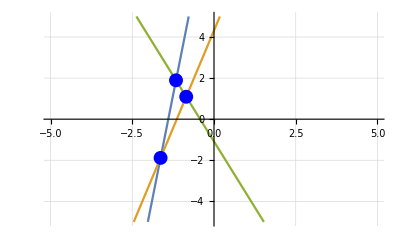

```mathematica
App2[W1]
```

```mathematica
Layer1[X_List,W_List,ϕ_]:=neuron[X,#,ϕ]&/@W//N
```

```mathematica
Layer2[X_List,W_,ϕ_]:=neuron[X,W,ϕ]
```

```mathematica
perceptron2[X_List,W_List,ϕ_]:=Layer2[Layer1[X,W⟦1⟧,ϕ],W⟦2⟧,ϕ]
```

Задаем рандомные веса

```mathematica
Wr1={RandomReal[{-1,1},3],RandomReal[{-1,0},3],RandomReal[{0,1},3]};
Wr2=RandomReal[{-1,0},4];
```

Задаем эпохи.

```mathematica
period2={};
For[n=500,n≥0,n--,AppendTo[period2,RandomSample[Teach111]]];
```

Следующая функция необходима для коррекции весов 1 и 2 слоя методом обратного распространения ошмбки

```mathematica
App3[ans_,wes_,FA_]:=(
res1=wes⟦1⟧;
res2=wes⟦2⟧;
For[i=1,i≤Length[ans],i++,
γ=0.5;
net2net3net4=Layer1[ans⟦i,1⟧,res1,sigm];
out=AppendTo[net2net3net4,1];
net5=perceptron2[ans⟦i,1⟧,{res1,res2},sigm];
E1=(ans⟦i,2⟧-net5);
δ5=(ans⟦i,2⟧-net5)*1/2(1-net5)(1+net5);
δ234=Table[δ5*res2⟦j⟧*1/2(1-out⟦j⟧)(1+out⟦j⟧),{j,1,Length[res2]}];
       Δwl1=Table[δ234⟦m⟧*Append[ans⟦i,1⟧,1],{m,1,3}]//N;
Δwl2=δ5*out;
res1=res1+γ*Δwl1;
res2=res2+γ*Δwl2;];
{res1,res2}
)
```

```mathematica
App3[period2⟦3⟧,{Wr1,Wr2},sigm]
```

{{{-408.618,168.871,473.112},{471.737,435.234,76.7993},{692.857,279.517,-332.101}},{303.059,-330.342,-341.273,4.49812}}

```mathematica
net2net3net4=Layer1[Teacher⟦1,1⟧,Wr1,sigm]
out=AppendTo[net2net3net4,1]
net5=perceptron2[Teacher⟦1,1⟧,{Wr1,Wr2},sigm]
δ5=(Teacher⟦1,2⟧-net5)*1/2(1-net5)(1+net5)
δ234=Table[δ5*Wr2⟦i⟧*1/2(1-out⟦i⟧)(1+out⟦i⟧),{i,1,Length[Wr2]}]
       Δwl1=Table[δ234⟦i⟧*Append[Teacher⟦1,1⟧,1],{i,1,3}]//N
Δwl2=δ5*out
Wr1=Wr1+Δwl1
Wr2=Wr2+Δwl2
```

{-0.906858,1.48963,1.23345}

{-0.906858,1.48963,1.23345,1}

-1.6606

-0.580526

{0.011232,-0.337504,-0.127156,0.}

{{-0.022464,-0.022464,0.011232},{0.675007,0.675007,-0.337504},{0.254312,0.254312,-0.127156}}

{0.526455,-0.864768,-0.716049,-0.580526}

{{-0.023455,0.16427,-0.49938},{-0.179083,0.200057,-1.00742},{0.191488,0.149233,0.89488}}

{0.308584,-1.81863,-1.55624,-1.40469}

Основная идея метода обратного распространения ошибки состоит в распространении сигналов ошибки от выходов сети к её входам,в направлении,обратном прямому распространению сигналов в обычном режиме работы.  Можно сделать вывод что метод обратного распространения ошибки позволяет, не зная весов первоначальных(скрытых) слоев, корректировать все веса всех слоев, опираясь только на ошибку последнего.